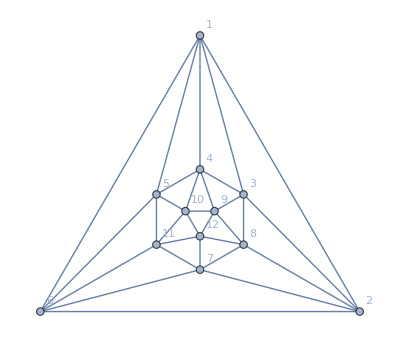

```mathematica
Graph[plantri[[1]],GraphLayout->"TutteEmbedding",VertexLabels->"Name"]
```

```mathematica
FindNeighbours[Graph[plantri[[1]]],{9}]
```

{3,4,8,10,12}

```mathematica
FindNeighbours[g_,vertices_]:=Block[{temp},
temp=VertexDelete[NeighborhoodGraph[g,vertices],vertices];
VertexList[temp]
]
```

```mathematica
AltitudeLines[g_,v_]:=Block[{subG, result={},result2={}, currentVertices, keep, cycle},
subG=g;
currentVertices={v};
While[Length[EdgeList[subG]]>1,keep=FindNeighbours[subG,currentVertices];

AppendTo[result2,currentVertices];
If[Length[keep]>1,
cycle=DiscoverCycle[subG,keep];
(*Print[{keep,cycle}];*)
AppendTo[result,cycle],
Print[keep];
AppendTo[result2,keep];
];


subG=VertexDelete[subG,currentVertices];
currentVertices=keep;
];
{Graph[g,
VertexLabels->"Name",
VertexSize->Large,
EdgeStyle->Flatten[Table[Map[#->IndexToColor[k]&,result[[k]]],{k,1,Length[result]}]],
VertexStyle->Flatten[Table[Map[#->IndexToColor[Mod[k+6,4]+1]&,result2[[k]]],{k,1,Length[result2]}]],
ImageSize->800
],
result,
result2
}

]
```

{11}

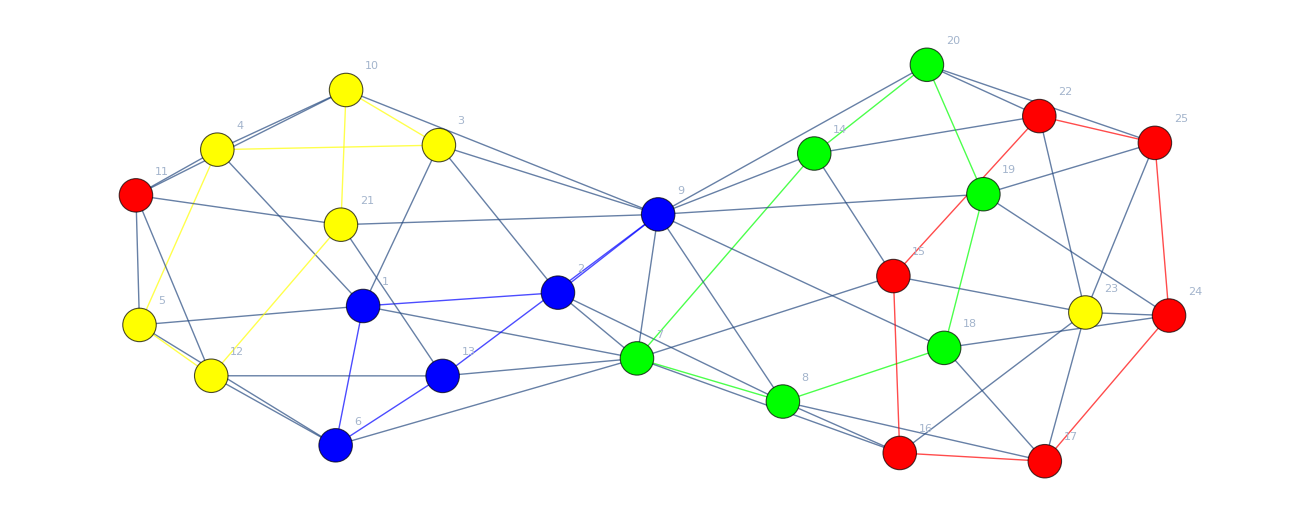
{-Graphics-,{{15<->16,16<->17,17<->24,24<->25,25<->22,15<->22},{7<->8,8<->18,18<->19,19<->20,20<->14,7<->14},{1<->2,2<->9,9<->13,13<->6,1<->6},{3<->4,4<->5,5<->12,12<->21,21<->10,3<->10}},{{23},{15,16,17,22,24,25},{7,14,8,18,20,19},{1,2,6,9,13},{3,4,5,12,10,21},{11}}}

```mathematica
AltitudeLines[Graph[plantri[[24534]]],23]
```

{}

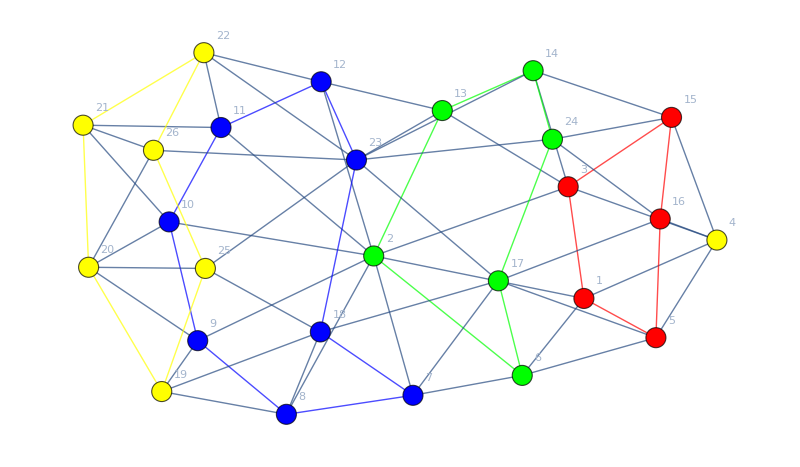
{-Graphics-,{{1<->3,3<->15,15<->16,16<->5,1<->5},{2<->6,6<->17,17<->24,24<->14,14<->13,2<->13},{7<->8,8<->9,9<->10,10<->11,11<->12,12<->23,23<->18,7<->18},{19<->20,20<->21,21<->22,22<->26,26<->25,19<->25}}}

```mathematica
AltitudeLines[Graph[plantri[[90000]]],4]
```

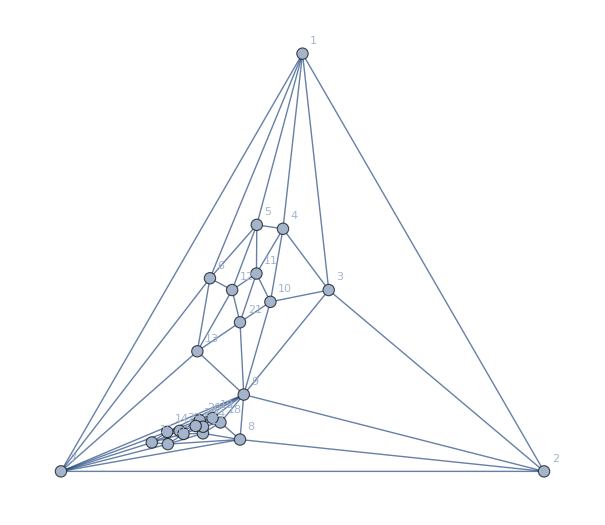

```mathematica
Graph[plantri[[24534]],
GraphLayout->"TutteEmbedding",
VertexLabels->"Name"]
```